Mean of the delay till absorption: 0.00106179 | 0.0011947 | 0.00134111 | 0.00150244 | 0.00168022
0.0011271 | 0.00141997 | 0.00177352 | 0.00220075 | 0.00271744
0.00119586 | 0.00167761 | 0.00231222 | 0.0031505 | 0.00426009
0.00126799 | 0.0019694 | 0.00297423 | 0.00442134 | 0.00651314
0.00134339 | 0.0022971 | 0.0037786 | 0.00609958 | 0.00975575
0.00142199 | 0.00266244 | 0.00474654 | 0.00829096 | 0.014363
0.00150368 | 0.00306706 | 0.00590138 | 0.0111236 | 0.0208322
0.00158837 | 0.00351254 | 0.00726856 | 0.014751 | 0.0298134
0.00167597 | 0.00400034 | 0.00887557 | 0.0193549 | 0.0421459
0.00176637 | 0.00453178 | 0.0107517 | 0.0251483 | 0.0588978
0.00185946 | 0.00510802 | 0.012928 | 0.0323774 | 0.0814112

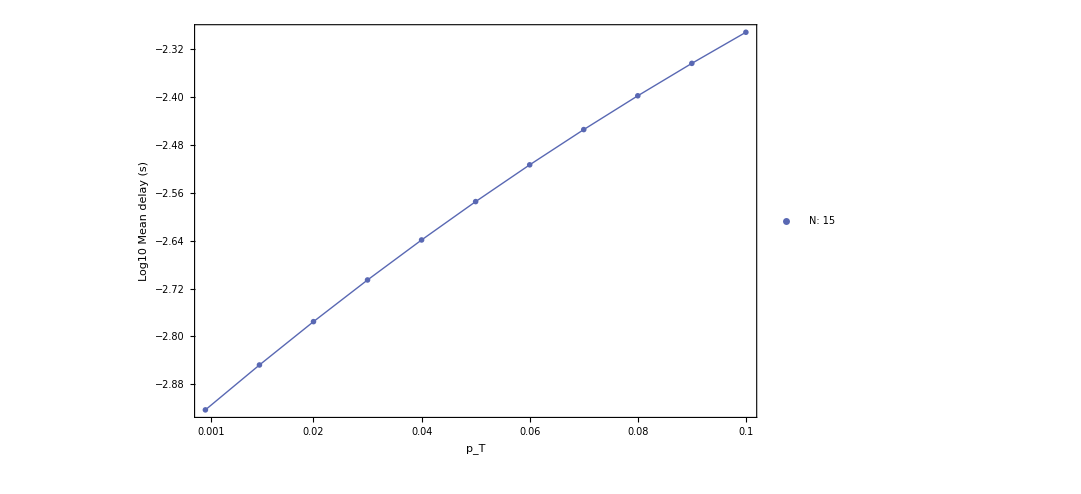

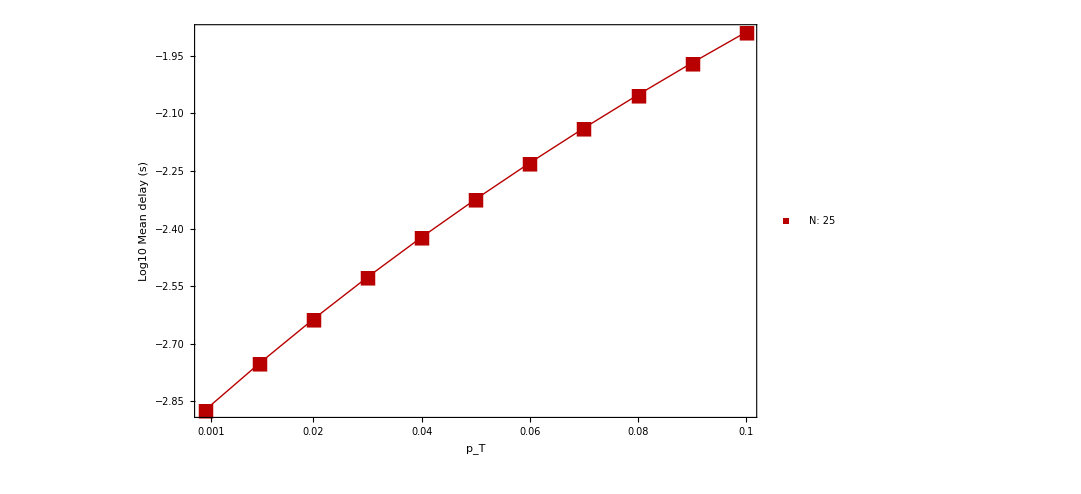

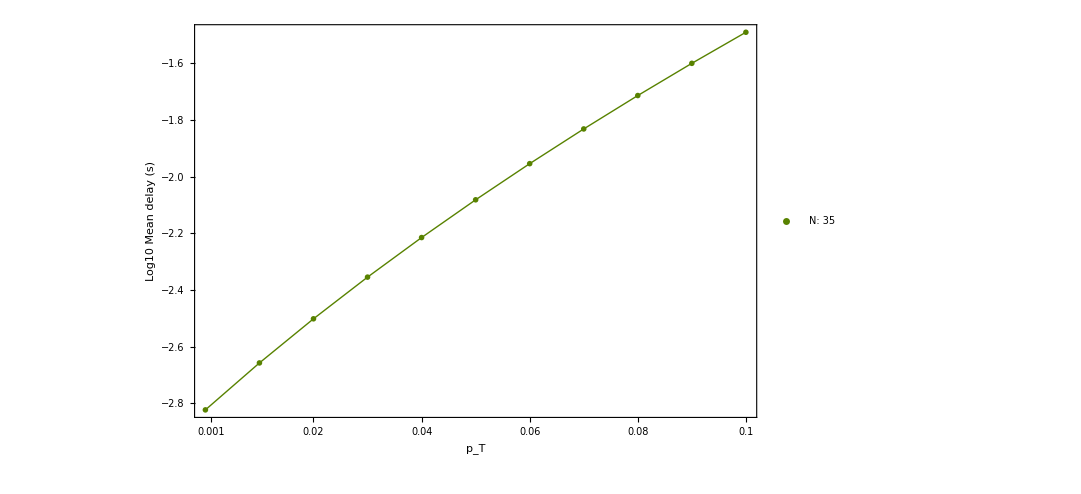

ColorData::notent: 95 is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

ColorData::notent: Directive[AbsoluteThickness[1], 95] is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

ColorData::notent: {AbsoluteThickness[1], 95} is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

General::stop: Further output of ColorData :: notent will be suppressed during this calculation.

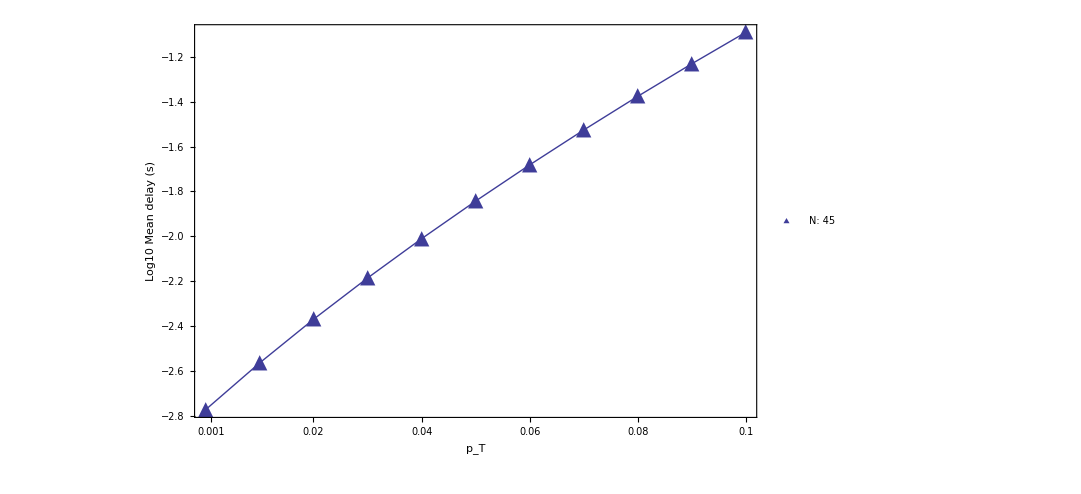

28.3465

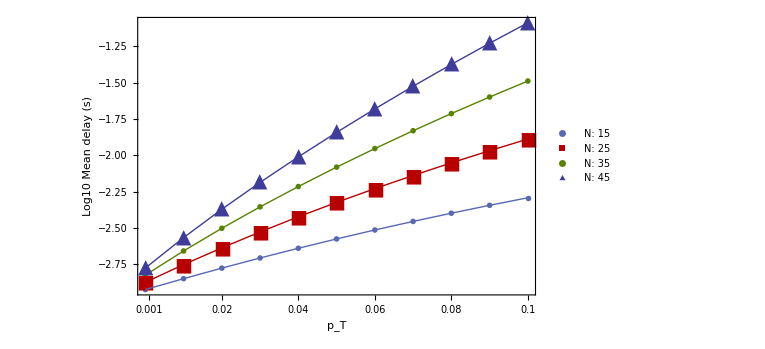

Compare-MeanDelay-log.eps

Mean of the delay till absorption: 0.696527 | 24.3737 | 785.571
0.682047 | 23.3496 | 732.402
0.670481 | 22.3254 | 682.591
0.65918 | 21.3515 | 635.985
0.648142 | 20.4072 | 592.387
0.637366 | 19.5031 | 551.612
0.626847 | 18.637 | 513.501
0.616585 | 17.8075 | 477.893
0.606576 | 17.0131 | 444.564
0.596817 | 16.2526 | 413.474
0.587306 | 15.5248 | 384.43
0.578039 | 14.8284 | 357.318
0.569013 | 14.1622 | 332.02
0.560226 | 13.5252 | 308.421
0.551672 | 12.9161 | 286.415
0.543351 | 12.3339 | 265.901
0.535256 | 11.7777 | 246.784
0.527387 | 11.2463 | 228.977
0.519737 | 10.7389 | 212.394
0.512305 | 10.2544 | 196.957
0.505086 | 9.792 | 182.592
0.498077 | 9.3508 | 169.23
0.491274 | 8.92995 | 156.805
0.484674 | 8.52863 | 145.256
0.478272 | 8.14603 | 134.525
0.472066 | 7.78141 | 124.558
0.46605 | 7.43401 | 115.303
0.460223 | 7.10311 | 106.714
0.45458 | 6.78804 | 98.7461
0.449117 | 6.48812 | 91.3564
0.443831 | 6.20271 | 84.5062
0.438719 | 5.93118 | 78.1584
0.433776 | 5.67294 | 72.2786
0.429 | 5.42741 | 66.8344
0.424387 | 5.19403 | 61.7957
0.419933 | 4.97227 | 57.134
0.415636 | 4.7616 | 52.8228
0.411492 | 4.56154 | 48.8375
0.407498 | 4.3716 | 45.1547
0.40365 | 4.19132 | 41.7529
0.399946 | 4.02026 | 38.6119
0.396382 | 3.858 | 35.7128
0.392956 | 3.70412 | 33.038
0.389664 | 3.55822 | 30.571
0.386504 | 3.41995 | 28.2965
0.383473 | 3.28892 | 26.2003
0.380568 | 3.1648 | 24.269
0.377787 | 3.04726 | 22.4903
0.375126 | 2.93597 | 20.8526
0.372584 | 2.83063 | 19.3452

```mathematica
(*
 DO:
 - no collision-related losses;
  - losses of retransmission requests due to wireless medium;
  - losses of informational packets due to wireless medium
GET:
- PMF on the number of retr. attempts to deliver a packet and message to all the stations;
  - PMF and CDF of the delay;
  - mean delay till all get the packet;
*)

(* Maxumun number of retransmissions, assumed to be infinity but this is enough *)
stepsMax=10;

(* Range of packet loss values *)
Pinit=0.01;
Pend  =0.11;
Pstep=0.01;

(* Number of stations *)
Ninit=5;
Nend=46;
Nstep=10;

(* Loss probability of retransmission packet *)

Unprotect[Power];
Power[0,0]=1;
Protect[Power];

pR=0;

(* Probability of channel access for data and retr. req. packet, F - forward data packet, R - retr. packet *)
rT=0.2;
rQ=0.2;

(* Duration of a time slot *)
slt=0.00001;

(*Time to transmit the data packet (Tt) and retrnamission request (Tq), respectively, Tq<<Tt as data packets is usually longer *)
Tt= 0.001;
Tq= 0.0001;

(* Time to wait to get the packet of interest as a result of the sent request *)

Tconst = 0.0012;

(* Arrays to store PDF, CDF, Variance, Mean and quantile of the number of steps till absorbtion *)
singlePMFArray=Table[0*i*j*g*n,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1},{g,1,2,1},{n,1,stepsMax}];
singleCDFArray=Table[0*i*j*g*n,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1},{g,1,2,1},{n,1,stepsMax}];

singleVarArray=Table[0*i*j,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1}];
singleMeanArray=Table[0*i*j,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1}];


(* Arrays to store PDF, Mean and quantile of delay till absorbtion *)
singlePMFDelay=Table[0*i*j*g*n,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1},{g,1,2,1},{n,1,stepsMax}];
singleMeanDelay=Table[0*i*j,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1}];


(* Definiting Binomial distribution *)
BD[n_,p_,i_]:=Binomial[n,i]*(p^i)*(1-p)^n/(1-p)^i;

i=1;
j=1;

Do[
Do[

(* PARAMETERIZATION *)

(* Matrix Q of the absorbing Markov chain chain: jumping between transient states *)
Q=Table[0*k*n,{n,1,currN},{k,1,currN}];


For[n=1,n<currN+1,n++,
For[k=1,k<currN+1,k++,
If[k==n,If[n==currN,Part[Q,n,k]=Power[currP,n],Part[Q,n,k]=Power[pR,currN-n]+(1-Power[pR,currN-n])*Power[currP,n]]];
If[k<n,If[n==currN,Part[Q,n,k]=BD[n,currP,k],Part[Q,n,k]=(1-Power[pR,currN-n])*BD[n,currP,k]]];
];
];

(* Print["Matrix Q: ",TableForm[Q]]; *)

(* Defining vector t of the chain: absorbtion from every state *)
t=Table[0*n,{n,1,currN}];

For[n=1,n<currN+1,n++,
If[n≠currN,Part[t,n]=(1-Power[pR,currN-n])*(Power[1-currP,n]),Part[t,n]=Power[1-currP,currN]];
];

(* Print["vector t: ",TableForm[t]]; *)

(* Defining initial state probability vector: we always start with N stations not having a packet *)
v=Table[0*n,{n,1,currN}];
Part[v,currN]=1;

(* Print["vector v: ",TableForm[v]]; *)

(* COMPUTING METRICS FOR A SINGLE PACKET *)

(* Supplementary entities *)
e=Table[0*n+1,{n,1,currN}];

(* Print["vector e: ",TableForm[e]]; *)

(* PMF of the number of steps till absrobtion: gives PMF of the delay *)
stepsPMF=Table[v.If[n≠0,MatrixPower[Q,n],IdentityMatrix[currN]].t,{n,0,stepsMax}];

(* Print["stepsPMF: ",TableForm[stepsPMF]]; *)

(* Testing whether PMF sums up to one, if not increase the stepsMax*)
If[Sum[Part[stepsPMF,n],{n,0,stepsMax}]<0.99||Sum[Part[stepsPMF,n],{n,0,stepsMax}]>1.01,Print["PMF does not sum up to 1!"]];

(* Print["PMF sum to 1? ",TableForm[Sum[Part[stepsPMF,n],{n,1,stepsMax}]]]; *)

(* CDF of the number of steps till absrobtion: gives CDF of the delay *)

stepsCDF=Table[Sum[Part[stepsPMF,n],{n,1,k}],{k,1,stepsMax}];
(* Mean number of steps before absorbtion: gives mean delay *)
stepsMean=Sum[Part[stepsPMF,n]*n,{n,1,stepsMax}];

(* Print["steps Mean: ",TableForm[stepsMean]]; *)

(* Variance of the number of steps *)
stepsVar=Sum[Part[stepsPMF,n]*Power[(n-stepsMean),2],{n,1,stepsMax}];

(* Print["steps Variance: ",TableForm[stepsVar]]; *)

(* We can also get probabilities that k, k=1,2,..,N stations not having a packet after k step this is a vector: v*Q^{k} *)

(* Computing the Fundamental matrix *)
Z=Inverse[IdentityMatrix[currN]-Q];

(* Computing hi as the probability of being in the arbitrary state i after original transmission of the packet *)
(*h =Table [ PDF[BinomialDistribution[currN,pR],n],{n,0,currN}];*)

(* Probability of visiting a transient state j when starting in transient state i *)
Zdq=DiagonalMatrix[Diagonal[Z]];
visitPrMatrix=(Z-IdentityMatrix[currN]).Inverse[Zdq];

 (* Print["Matrix Z: ",TableForm[Z]]; *)

(* Print["Visits V: ",TableForm[visitPrMatrix]]; *)

(* CONDITIONAL DELAY IN A CERTAIN STATE *)
(* Array for conditional delays for failure and overall *)
condDelayFail=Table[0,{k,1,currN}];
condDelayAll=Table[0,{k,1,currN}];

(* Computing conditional delays for states starting from 1 to N-1: in case of failure *)
For [n=1,n<currN+1,n++,
  Part[condDelayFail,n] = Tconst;
];


(* Computing the mean delay in the arbitrary state i: for non-zero request packet loss probabilities *)

For [n=1,n<currN+1,n++,
Part[condDelayAll,n]= 1/Part[Q,n,n]*Part[condDelayFail,n]+((1/rQ)*slt) + Tq  +((1/rT)*slt) + Tt;
];

(*
For [i=1,i<currN+1,i++,
 Print["Conditional delay all ",i,": ",TableForm[Part[condDelayAll,i]]];
];
*)

(* Computing the mean delay till absorption *)

overallDelay =Tt + Sum[BD[currN,currP,n]*Part[condDelayAll,k]*Part[visitPrMatrix,n,k],{n,1,currN},{k,1,n}];

(*  Print["Overall Delay: ",TableForm[overallDelay]]; *)

(* Storing PMF of the number of steps to global matrices*)
For[n=1,n<stepsMax+1,n++,
Part[singlePMFArray,i,j,2,n]=Part[stepsPMF,n];
Part[singlePMFArray,i,j,1,n]=n;
];

(* Print["PMF of steps till absorption: ",TableForm[singlePMFArray]]; *)

(* Storing CDF of the number of steps to global matrices*)
For[n=1,n<stepsMax+1,n++,
Part[singleCDFArray,i,j,2,n]=Part[stepsCDF,n];
Part[singleCDFArray,i,j,1,n]=n;
];

(* Print["CDF of steps till absorption: ",TableForm[singleCDFArray]]; *)

(* Storing Variance of the number of steps to global matrices*)
Part[singleVarArray,i,j]=stepsVar;
(* Print["Variance of steps till absorption: ",TableForm[singleVarArray]]; *)


(* Storing Mean of the number of steps to global matrices*)
Part[singleMeanArray,i,j]=stepsMean;
(* Print["Mean of the number of steps till absorption: ",TableForm[singleMeanArray]]; *)


(* Storing Mean of the delay to global matrices *)
Part[singleMeanDelay,i,j]=overallDelay;
 (*  Print["Mean of the delay till absorption: ",TableForm[singleMeanDelay]]; *)

(* PMF and CDF of delay not for this version *)


(* ENDING THE CYCLES *)
i++;,
{currP,Pinit,Pend,Pstep}];

i=1;
j++;,


{currN,Ninit,Nend,Nstep}];


 Print["Mean of the delay till absorption: ",TableForm[singleMeanDelay]]; 
(*
PlotLegends ->Placed [LineLegend[{"packet_loss: 0.001"}],{Right}]
*)
(*
Export["myimage2.eps",ListPlot[{Part[singleMeanDelay,2,1],Part[singleMeanDelay,2,2],Part[singleMeanDelay,2,3],Part[singleMeanDelay,2,4],Part[singleMeanDelay,2,5],Part[singleMeanDelay,2,6],Part[singleMeanDelay,2,7],Part[singleMeanDelay,2,8],Part[singleMeanDelay,2,9],Part[singleMeanDelay,2,10],Part[singleMeanDelay,2,11]},Joined->True,Filling->None,Frame->True ,FrameLabel->{Style["Index of no. of receivers",Blue,Small],Style["Mean Delay",Blue,Small]}]]
*)



(*
kplot = ListPlot[{Part[singleMeanDelay,12,1],Part[singleMeanDelay,12,2],Part[singleMeanDelay,12,3],Part[singleMeanDelay,12,4],Part[singleMeanDelay,12,5],Part[singleMeanDelay,12,6],Part[singleMeanDelay,12,7],Part[singleMeanDelay,12,8],Part[singleMeanDelay,12,9],Part[singleMeanDelay,12,10]},Joined->True,Filling->None,Frame->True ,FrameLabel->{Style["Index of no. of receivers",Blue,Small],Style["Mean Delay",Blue,Small]},PlotStyle->Blue,PlotLegends ->Placed [LineLegend[{"packet_loss: 0.0001"}],{Top,Right}]]

cplot = ListPlot[{Part[singleMeanDelay,6,1],Part[singleMeanDelay,6,2],Part[singleMeanDelay,6,3],Part[singleMeanDelay,6,4],Part[singleMeanDelay,6,5],Part[singleMeanDelay,6,6],Part[singleMeanDelay,6,7],Part[singleMeanDelay,6,8],Part[singleMeanDelay,6,9],Part[singleMeanDelay,6,10]},Joined->True,Filling->None,Frame->True ,FrameLabel->{Style["Index of no. of receivers",Blue,Small],Style["Mean Delay",Blue,Small]},PlotStyle->Green,PlotLegends ->Placed [LineLegend[{"packet_loss: 0.06"}],{Top,Right}]]

splot = ListPlot[{Part[singleMeanDelay,1,1],Part[singleMeanDelay,1,2],Part[singleMeanDelay,1,3],Part[singleMeanDelay,1,4],Part[singleMeanDelay,1,5],Part[singleMeanDelay,1,6],Part[singleMeanDelay,1,7],Part[singleMeanDelay,1,8],Part[singleMeanDelay,1,9],Part[singleMeanDelay,1,10]},Joined->True,Filling->None,Frame->True ,FrameLabel->{Style["Index of no. of receivers",Blue,Small],Style["Mean Delay",Blue,Small]},PlotStyle->Red,PlotLegends ->Placed [LineLegend[{"packet_loss: 0.16"}],{Top,Right}]]

Export["MeanDelay.eps",Show[cplot,kplot,splot]]
*)

(*
kplot = ListPlot[{Part[singleMeanDelay,12,1],Part[singleMeanDelay,12,2],Part[singleMeanDelay,12,3],Part[singleMeanDelay,12,4],Part[singleMeanDelay,12,5],Part[singleMeanDelay,12,6],Part[singleMeanDelay,12,7],Part[singleMeanDelay,12,8],Part[singleMeanDelay,12,9],Part[singleMeanDelay,12,10]},Joined->True,Filling->None,Frame->True ,FrameLabel->{Style["Index of no. of receivers",Black,Large],Style["Mean Delay",Black,Large]},PlotMarkers->markers1,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[55,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},PlotLegends->PointLegend[Row[{"packet_loss: 0.0001",#1}]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->17,LabelStyle->{GrayLevel[0.3],20}],BaseStyle->{FontSize->25}]

cplot = ListPlot[{Part[singleMeanDelay,6,1],Part[singleMeanDelay,6,2],Part[singleMeanDelay,6,3],Part[singleMeanDelay,6,4],Part[singleMeanDelay,6,5],Part[singleMeanDelay,6,6],Part[singleMeanDelay,6,7],Part[singleMeanDelay,6,8],Part[singleMeanDelay,6,9],Part[singleMeanDelay,6,10]},Joined->True,Filling->None,Frame->True ,FrameLabel->{Style["Index of no. of receivers",Black,Large],Style["Mean Delay",Black,Large]},PlotMarkers->markers1,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[75,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},PlotLegends->PointLegend[Row[{"packet_loss: 0.06",#1}]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->17,LabelStyle->{GrayLevel[0.3],20}],BaseStyle->{FontSize->25}]

splot = ListPlot[{Part[singleMeanDelay,1,1],Part[singleMeanDelay,1,2],Part[singleMeanDelay,1,3],Part[singleMeanDelay,1,4],Part[singleMeanDelay,1,5],Part[singleMeanDelay,1,6],Part[singleMeanDelay,1,7],Part[singleMeanDelay,1,8],Part[singleMeanDelay,1,9],Part[singleMeanDelay,1,10]},Joined->True,Filling->None,Frame->True ,FrameLabel->{Style["Index of no. of receivers",Black,Large],Style["Mean Delay",Black,Large]},PlotMarkers->markers1,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[35,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},PlotLegends->PointLegend[Row[{"packet_loss: 0.16",#1}]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->17,LabelStyle->{GrayLevel[0.3],20}],BaseStyle->{FontSize->25}]


cm=72/2.54 (*centimetres*)


Export["New-MeanDelay.eps",Show[cplot,kplot,splot,ImageSize->20 cm]]
*)
(*
kplot = ListPlot[Evaluate[{Part[singleMeanDelay,16,1],Part[singleMeanDelay,16,2],Part[singleMeanDelay,16,3],Part[singleMeanDelay,16,4],Part[singleMeanDelay,16,5],Part[singleMeanDelay,16,6],Part[singleMeanDelay,16,7],Part[singleMeanDelay,12,8],Part[singleMeanDelay,12,9],Part[singleMeanDelay,12,10]},Filling->None,Frame->True ,FrameLabel->{Style["no. of receivers",Black,Large],Style["Mean Delay",Black,Large]},PlotMarkers->markers1,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[55,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotLegends->Placed[PointLegend[Row[{Subscript[p,T],": 0.0001"#}]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->17,LabelStyle->{GrayLevel[0.3],20}],{0.72,0.9}]],BaseStyle->{FontSize->25}]

cplot = ListPlot[Evaluate[{Part[singleMeanDelay,6,1],Part[singleMeanDelay,6,2],Part[singleMeanDelay,6,3],Part[singleMeanDelay,6,4],Part[singleMeanDelay,6,5],Part[singleMeanDelay,6,6],Part[singleMeanDelay,6,7],Part[singleMeanDelay,6,8],Part[singleMeanDelay,6,9],Part[singleMeanDelay,6,10]},Filling->None,Frame->True ,FrameLabel->{Style["no. of receivers",Black,Large],Style["Mean Delay",Black,Large]},PlotMarkers->markers1,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[75,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotLegends->Placed[PointLegend[Row[{Subscript[p,T],": 0.05"#}]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->17,LabelStyle->{GrayLevel[0.3],20}],{0.7,0.8}]],BaseStyle->{FontSize->25}]

splot = ListPlot[Evaluate[{Part[singleMeanDelay,1,1],Part[singleMeanDelay,1,2],Part[singleMeanDelay,1,3],Part[singleMeanDelay,1,4],Part[singleMeanDelay,1,5],Part[singleMeanDelay,1,6],Part[singleMeanDelay,1,7],Part[singleMeanDelay,1,8],Part[singleMeanDelay,1,9],Part[singleMeanDelay,1,10]},Filling->None,Frame->True ,FrameLabel->{Style["no. of receivers",Black,Large],Style["Mean Delay",Black,Large]},PlotMarkers->markers1,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[35,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotLegends->Placed[PointLegend[Row[{Subscript[p,T],": 0.15"#}]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->17,LabelStyle->{GrayLevel[0.3],20}],{0.7,0.7}]],BaseStyle->{FontSize->25}]

cm=72/2.54 (*centimetres*)

Show[cplot,kplot,splot,ImageSize->20 cm]
Export["Newly-added-MeanDelay.eps",Show[cplot,kplot,splot,ImageSize->20 cm]]
*)

(*
kplot = ListPlot[Evaluate[Log[10,{Part[singleMeanDelay,60,1],Part[singleMeanDelay,50,1],Part[singleMeanDelay,40,1],Part[singleMeanDelay,30,1],Part[singleMeanDelay,20,1],Part[singleMeanDelay,25,1],Part[singleMeanDelay,24,1],Part[singleMeanDelay,23,1],Part[singleMeanDelay,22,1],Part[singleMeanDelay,21,1],Part[singleMeanDelay,20,1],Part[singleMeanDelay,19,1],Part[singleMeanDelay,18,1],Part[singleMeanDelay,17,1],Part[singleMeanDelay,16,1],Part[singleMeanDelay,15,1],Part[singleMeanDelay,14,1],Part[singleMeanDelay,13,1],Part[singleMeanDelay,12,1],Part[singleMeanDelay,11,1],Part[singleMeanDelay,10,1],Part[singleMeanDelay,9,1],Part[singleMeanDelay,8,1],Part[singleMeanDelay,7,1],Part[singleMeanDelay,6,1],Part[singleMeanDelay,5,1],Part[singleMeanDelay,4,1],Part[singleMeanDelay,3,1],Part[singleMeanDelay,2,1],Part[singleMeanDelay,1,1]}],Filling->None,Frame->True ,FrameLabel->{Style["Index of "Subscript[p,T],Black,Large],Style["Mean Delay",Black,Large]},PlotMarkers->markers1,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[55,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->All,     PlotLegends->Placed[PointLegend[Row[{"N: 5"#}]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->17,LabelStyle->{GrayLevel[0.3],20}],{0.69,0.9}]],BaseStyle->{FontSize->25}]

cplot = ListPlot[Evaluate[Log[10,{Part[singleMeanDelay,17,2],Part[singleMeanDelay,16,2],Part[singleMeanDelay,15,2],Part[singleMeanDelay,14,2],Part[singleMeanDelay,13,2],Part[singleMeanDelay,12,2],Part[singleMeanDelay,11,2],Part[singleMeanDelay,10,2],Part[singleMeanDelay,9,2],Part[singleMeanDelay,8,2],Part[singleMeanDelay,7,2],Part[singleMeanDelay,6,2],Part[singleMeanDelay,5,2],Part[singleMeanDelay,4,2],Part[singleMeanDelay,3,2],Part[singleMeanDelay,2,2],Part[singleMeanDelay,1,2]}],Filling->None,Frame->True ,FrameLabel->{Style["Index of "Subscript[p,T],Black,Large],Style["Mean Delay",Black,Large]},PlotMarkers->markers1,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[75,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->All,PlotLegends->Placed[PointLegend[Row[{"N: 10"#}]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->17,LabelStyle->{GrayLevel[0.3],20}],{0.7,0.8}]],BaseStyle->{FontSize->25}]

splot = ListPlot[Evaluate[Log[10,{Part[singleMeanDelay,17,3],Part[singleMeanDelay,16,3],Part[singleMeanDelay,15,3],Part[singleMeanDelay,14,3],Part[singleMeanDelay,13,3],Part[singleMeanDelay,12,3],Part[singleMeanDelay,11,3],Part[singleMeanDelay,10,3],Part[singleMeanDelay,9,3],Part[singleMeanDelay,8,3],Part[singleMeanDelay,7,3],Part[singleMeanDelay,6,3],Part[singleMeanDelay,5,3],Part[singleMeanDelay,4,3],Part[singleMeanDelay,3,3],Part[singleMeanDelay,2,3],Part[singleMeanDelay,1,3]}],Filling->None,Frame->True ,FrameLabel->{Style["Index of :"Subscript[p,T],Black,Large],Style["Mean Delay",Black,Large]},PlotMarkers->markers1,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[35,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->All,PlotLegends->Placed[PointLegend[Row[{"N: 15"#}]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->17,LabelStyle->{GrayLevel[0.3],20}],{0.7,0.7}]],BaseStyle->{FontSize->25}]

cm=72/2.54 (*centimetres*)

Show[cplot,kplot,splot,ImageSize->20 cm]
Export["Newly-added-MeanDelay.eps",Show[cplot,kplot,splot,ImageSize->100 cm,PlotRange->All]]
*)
(*
markers1 = {{-Graphics-, 0.04}};

kplot = ListPlot[Evaluate[Log[10,{Part[singleMeanDelay,1,1],Part[singleMeanDelay,10,1],Part[singleMeanDelay,20,1],Part[singleMeanDelay,30,1],Part[singleMeanDelay,40,1],Part[singleMeanDelay,50,1]}],Filling->None,DataRange->{0.0,0.5},Frame->True ,FrameTicks->{{Automatic,None},{{0.0001,0.1,0.2,0.3,0.4,0.5},None}},FrameLabel->{Style[Subscript[p,T],Black,25],Style["Mean Delay (s)",Black,25]},PlotMarkers->markers1,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[85,"ColorList"]),ImageSize->1000,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->All,     PlotLegends->Placed[PointLegend[Row[{"N: 5"#}]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->18,LabelStyle->{GrayLevel[0.1],20}],{0.11,0.9}]],BaseStyle->{FontSize->30}]

markers2 = { {-Graphics-, 0.04}};

cplot = ListPlot[Evaluate[Log[10,{Part[singleMeanDelay,1,2],Part[singleMeanDelay,10,2],Part[singleMeanDelay,20,2],Part[singleMeanDelay,30,2],Part[singleMeanDelay,40,2],Part[singleMeanDelay,50,2]}],Filling->None,DataRange->{0.0,0.5},Frame->True ,FrameTicks->{{Automatic,None},{{0.0001,0.1,0.2,0.3,0.4,0.5},None}},FrameLabel->{Style[Subscript[p,T],Black,25],Style["Mean Delay (s)",Black,25]},PlotMarkers->markers2,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[75,"ColorList"]),ImageSize->1000,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->All,PlotLegends->Placed[PointLegend[Row[{"N: 10"#}]&/@Range[4],LegendMarkers->markers2 ,LegendMarkerSize->18,LabelStyle->{GrayLevel[0.1],20}],{0.12,0.8}]],BaseStyle->{FontSize->30}]

markers3 = { {-Graphics-, 0.04}};

splot = ListPlot[Evaluate[Log[10,{Part[singleMeanDelay,1,3],Part[singleMeanDelay,10,3],Part[singleMeanDelay,20,3],Part[singleMeanDelay,30,3],Part[singleMeanDelay,40,3],Part[singleMeanDelay,50,3]}],Filling->None,DataRange->{0.0,0.5},Frame->True ,FrameTicks->{{Automatic,None},{{0.0001,0.1,0.2,0.3,0.4,0.5},None}},FrameLabel->{Style[Subscript[p,T],Black,25],Style["Mean Delay (s)",Black,25]},PlotMarkers->markers3,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[Blue,"ColorList"]),ImageSize->1000,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->All,PlotLegends->Placed[PointLegend[Row[{"N: 15"#}]&/@Range[4],LegendMarkers->markers3 ,LegendMarkerSize->18,LabelStyle->{GrayLevel[0.1],20}],{0.12,0.7}]],BaseStyle->{FontSize->30}]

cm=72/2.54 (*centimetres*)

Show[cplot,kplot,splot,ImageSize->20 cm]
Export["Newly-added-MeanDelay-no-log.eps",Show[cplot,kplot,splot,ImageSize->20 cm,PlotRange->All]]
*)



markers3 = { {-Graphics-, 0.04}};

ssplot = ListPlot[Evaluate[Log[10,{Part[singleMeanDelay,1,2],Part[singleMeanDelay,2,2],Part[singleMeanDelay,3,2],Part[singleMeanDelay,4,2],Part[singleMeanDelay,5,2],Part[singleMeanDelay,6,2],Part[singleMeanDelay,7,2],Part[singleMeanDelay,8,2],Part[singleMeanDelay,9,2],Part[singleMeanDelay,10,2],Part[singleMeanDelay,11,2]}],Filling->None,DataRange->{0.0,0.1},Frame->True ,FrameTicks->{{Automatic,None},{{0.001,0.02,0.04,0.06,0.08,0.1},None}},FrameLabel->{Style[Subscript[p,T],Black,20],Style["Log10 Mean delay (s)",Black,20]},PlotMarkers->markers3,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[65,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->All ,  PlotLegends->Placed[PointLegend[Row[{"N: 15"#}]&/@Range[4],LegendMarkers->markers3 ,LegendMarkerSize->14,LabelStyle->{GrayLevel[0.1],19}],{0.1,0.9}]],BaseStyle->{FontSize->19}]

markers4 = {{■,19}};

kkplot = ListPlot[Evaluate[Log[10,{Part[singleMeanDelay,1,3],Part[singleMeanDelay,2,3],Part[singleMeanDelay,3,3],Part[singleMeanDelay,4,3],Part[singleMeanDelay,5,3],Part[singleMeanDelay,6,3],Part[singleMeanDelay,7,3],Part[singleMeanDelay,8,3],Part[singleMeanDelay,9,3],Part[singleMeanDelay,10,3],Part[singleMeanDelay,11,3]}],Filling->None,DataRange->{0.0,0.1},Frame->True ,FrameTicks->{{Automatic,None},{{0.001,0.02,0.04,0.06,0.08,0.1},None}},FrameLabel->{Style[Subscript[p,T],Black,25],Style["Log10 Mean delay (s)",Black,25]},PlotMarkers->markers4,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[85,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->All,        PlotLegends->Placed[PointLegend[Row[{"N: 25"#}]&/@Range[4],LegendMarkers->markers4 ,LegendMarkerSize->14,LabelStyle->{GrayLevel[0.1],19}],{0.1,0.82}]],BaseStyle->{FontSize->19}]



markers2 = { {-Graphics-, 0.04}};

ccplot = ListPlot[Evaluate[Log[10,{Part[singleMeanDelay,1,4],Part[singleMeanDelay,2,4],Part[singleMeanDelay,3,4],Part[singleMeanDelay,4,4],Part[singleMeanDelay,5,4],Part[singleMeanDelay,6,4],Part[singleMeanDelay,7,4],Part[singleMeanDelay,8,4],Part[singleMeanDelay,9,4],Part[singleMeanDelay,10,4],Part[singleMeanDelay,11,4]}],Filling->None,DataRange->{0.0,0.1},Frame->True ,FrameTicks->{{Automatic,None},{{0.001,0.02,0.04,0.06,0.08,0.1},None}},FrameLabel->{Style[Subscript[p,T],Black,25],Style["Log10 Mean delay (s)",Black,25]},PlotMarkers->markers2,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[75,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->All,   PlotLegends->Placed[PointLegend[Row[{"N: 35"#}]&/@Range[4],LegendMarkers->markers2 ,LegendMarkerSize->14,LabelStyle->{GrayLevel[0.1],19}],{0.1,0.74}]],BaseStyle->{FontSize->19}]

markers5 = {{▲,20}};

llplot = ListPlot[Evaluate[Log[10,{Part[singleMeanDelay,1,5],Part[singleMeanDelay,2,5],Part[singleMeanDelay,3,5],Part[singleMeanDelay,4,5],Part[singleMeanDelay,5,5],Part[singleMeanDelay,6,5],Part[singleMeanDelay,7,5],Part[singleMeanDelay,8,5],Part[singleMeanDelay,9,5],Part[singleMeanDelay,10,5],Part[singleMeanDelay,11,5]}],Filling->None,DataRange->{0.0,0.1},Frame->True ,FrameTicks->{{Automatic,None},{{0.001,0.02,0.04,0.06,0.08,0.1},None}},FrameLabel->{Style[Subscript[p,T],Black,25],Style["Log10 Mean delay (s)",Black,25]},PlotMarkers->markers5,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[95,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->All,     PlotLegends->Placed[PointLegend[Row[{"N: 45"#}]&/@Range[4],LegendMarkers->markers5 ,LegendMarkerSize->14,LabelStyle->{GrayLevel[0.1],19}],{0.1,0.66}]],BaseStyle->{FontSize->19}]



cm=72/2.54 (*centimetres*)

Show[ccplot,kkplot,ssplot ,llplot,ImageSize->20 cm]
Export["Compare-MeanDelay-log.eps",Show[ccplot,kkplot,ssplot,llplot,ImageSize->20 cm,PlotRange->All]]
```